# Madhava Series

## Accompanies Section 1.3 of Experimental Mathematics: A Computational Perspective by Matthew P. Richey and Matthew L. Wright

## Computing a Partial Sum

In this notebook we compute approximations to π using partial sums of the Taylor series for arctan(x). Specifically, for the infinite series

the partial sum is a finite sum

for some value maximum value m.

To compute this partial sum, we add up the first m terms of this series using a loop with an accumulator. Our accumulator, the variable acc in the code below, stores the running total as we add up the terms.

```mathematica
m=50; (* number of terms to add up *)
acc=0; (* accumulator, initialized to zero *)
Do[
(* Uncomment the following line to print out the values that we add ot the accumulator. Remember that print statements inside of a loop are helpful for debuggin! *)
(* Print[(-1)^(i+1)/(2i-1)];  *)
acc+=(-1)^(i+1)/(2i-1),
{i,1,m}]
```

The value 4×acc is our approximation of π. If we simply print this number, we’ll get a big fraction:

```mathematica
4*acc
```

3400605476464206445954873476681150352328/1089380862964257455695840764614254743075

We can also convert the result to a decimal number with any desired amount of digits. Here, we’ll ask for 20 digits:

```mathematica
N[4*acc, 20]
```

3.1215946525910104785

## Analyzing Accuracy

Let's find out how the accuracy of the approximation depends on the number of terms and recreate Table 1.2 in the text. For this, it is convenient to define a function (a Module, in Mathematica) that returns the m-term partial sum of the Madhava series.

It's important to consider the number type that the computer will use for this calculation. In the previous calculation we used fractions (exact values), but this may be rather slow if we want to add a large number of terms. The fastest option is to use floating-point numbers throughout the computation, but this provides a maximum of about 16 decimal digits and suffers from round-off error in repeated addition operations. A good middle ground is to use a large, but fixed, number of decimal digits throughout the calculation.

In the code below, we use Mathematica’s N function to specify that numbers are stored with 100 decimal digits of precision. This code is similar to Pseudocode 1.19 in the text.

```mathematica
madhavaSum[m_]:=Module[
{acc=0}, (* initialize the accumulator as a local variable *)
Do[
acc+=N[(-1)^(i+1)/(2i-1),100], (* note 100 decimal digits *)
{i,1,m}];
4*acc  (* return value *)
]
```

Try it out, computing the first ten partial sums. Mathematica’s Table function provides a convenient way to do this.

```mathematica
Table[madhavaSum[n],{n,1,10}]
```

{4.,2.66666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666667,3.46666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666667,2.8952380952380952380952380952380952380952380952380952380952380952380952380952380952380952380952381,3.33968253968253968253968253968253968253968253968253968253968253968253968253968253968253968253968254,2.97604617604617604617604617604617604617604617604617604617604617604617604617604617604617604617604618,3.28373848373848373848373848373848373848373848373848373848373848373848373848373848373848373848373848,3.01707181707181707181707181707181707181707181707181707181707181707181707181707181707181707181707182,3.25236593471887589534648358177769942475824828766005236593471887589534648358177769942475824828766005,3.04183961892940221113595726598822574054772197187057868172419256010587279937125138363528456407713374}

This same list could have been obtained using Mathematica’s Map function, which applies a function to input values in a specified list:

```mathematica
Map[madhavaSum,Range[1,10]]
```

{4.,2.66666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666667,3.46666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666667,2.8952380952380952380952380952380952380952380952380952380952380952380952380952380952380952380952381,3.33968253968253968253968253968253968253968253968253968253968253968253968253968253968253968253968254,2.97604617604617604617604617604617604617604617604617604617604617604617604617604617604617604617604618,3.28373848373848373848373848373848373848373848373848373848373848373848373848373848373848373848373848,3.01707181707181707181707181707181707181707181707181707181707181707181707181707181707181707181707182,3.25236593471887589534648358177769942475824828766005236593471887589534648358177769942475824828766005,3.04183961892940221113595726598822574054772197187057868172419256010587279937125138363528456407713374}

Now let's compute partial sums using more terms. First, we’ll make a list of values of m, each giving the number of terms for a partial sum that we will compute.

```mathematica
mVals=Range[100,1000,100]
```

{100,200,300,400,500,600,700,800,900,1000}

Now we will compute the partial sums for each value of m. We’ll print each partial sum to 20 decimal digits.

```mathematica
piVals=Map[madhavaSum,mVals];
N[piVals,20]
```

{3.1315929035585527643,3.1365926848388167504,3.1382593295155905679,3.1390926574960127215,3.1395926555897832386,3.1399259880805299605,3.1401640828900829243,3.1403426540780735348,3.1404815428216171263,3.140592653839792926}

Now we can compute the accuracy of each approximation using the log_10 method described in the text.

```mathematica
accuracy=N[-Log[10,Pi-piVals],3]
```

{2.,2.3,2.48,2.6,2.7,2.78,2.85,2.9,2.95,3.}

We can display these values in a table as follows:

```mathematica
TableForm[{mVals,N[piVals,10],accuracy},TableHeadings->{{"m","approx","accuracy"},None}]
```

m | 100 | 200 | 300 | 400 | 500 | 600 | 700 | 800 | 900 | 1000
approx | 3.131592904 | 3.136592685 | 3.13825933 | 3.139092657 | 3.139592656 | 3.139925988 | 3.140164083 | 3.140342654 | 3.140481543 | 3.140592654
accuracy | 2. | 2.3 | 2.48 | 2.6 | 2.7 | 2.78 | 2.85 | 2.9 | 2.95 | 3.

If we want to print the table vertically, like Table 1.2 in the text, then we can use the Transpose function like this:

```mathematica
TableForm[Transpose[{mVals,N[piVals,10],accuracy}],TableHeadings->{None,{"m","approx","accuracy"}}]
```

m | approx | accuracy
100 | 3.131592904 | 2.
200 | 3.136592685 | 2.3
300 | 3.13825933 | 2.48
400 | 3.139092657 | 2.6
500 | 3.139592656 | 2.7
600 | 3.139925988 | 2.78
700 | 3.140164083 | 2.85
800 | 3.140342654 | 2.9
900 | 3.140481543 | 2.95
1000 | 3.140592654 | 3.

We can also plot the accuracy. The following plot is similar to Figure 1.5 in the text. Note the use of DataRange to specify the range of values on the horizontal axis.

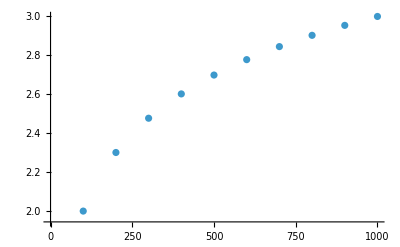

```mathematica
ListPlot[accuracy,DataRange->{100,1000},FrameLabel->{"number of terms","accuracy"}]
```

What is the shape of the accuracy plot? As in the text, we try to transform the accuracy values to make them linear. We will make plots similar to those in Figure 1.6 in the text. First, we try squaring the accuracy values, which is easy to do as follows.

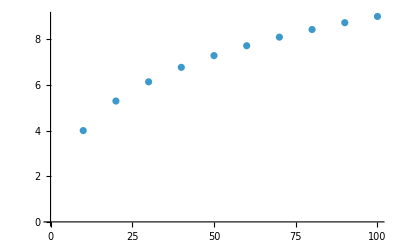

```mathematica
ListPlot[accuracy^2,DataRange->{10,100},FrameLabel->{"number of terms","accuracy^2"}]
```

The squared values are still not linear. Instead, let’s try raising 10 to the power of each accuracy value, as follows.

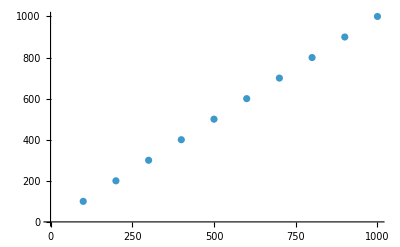

```mathematica
ListPlot[10^accuracy,DataRange->{100,1000},FrameLabel->{"number of terms","10^accuracy"}]
```

This looks quite linear. Hence we could comfortably conclude that the accuracy of the Madhava approximation grows logarithmically in the the number of terms.